## Assymmetric Molecule: Dispersion

```mathematica
ClearAll["Global`*"]
Ω[μ_]:=({{ω1[μ], -J12, 0}, {-J12, ω2[μ], -J23}, {0, -J23, ω3[μ]}});
```

```mathematica
ω1[μ_]:=ω0 +d1×μ + d2/2 μ^2;
ω2[μ_]:=ω0 +D1×(2μ) + D2/2(2μ)^2;
ω3[μ_]:=ω0+d1×μ + d2/2 μ^2 ;
```

```mathematica
d1 = 400;
D1 = 400/2.03;
d2 =-0.015;
D2 = 0.015;
ω0 = 0;
J12=2;
J23=2;
```

```mathematica
sortedEig[μ_]:=sortedEig[μ]=Module[{vals,vecs,pairs,fixSign},(*flip sign if the first component is negative*)
fixSign[v_]:=v/Sign[v[[1]]];
{vals,vecs}=Eigensystem[Ω[μ]];
vecs=fixSign/@vecs;
pairs=Transpose[{vals,vecs}];
SortBy[pairs,First]];
```

```mathematica
ωS[μ_]:=sortedEig[μ][[1,1]]
bS[μ_]:=Normalize[sortedEig[μ][[1,2]]];

ωC[μ_]:=sortedEig[μ][[2,1]];
bC[μ_]:=Normalize[sortedEig[μ][[2,2]]];

ωAS[μ_]:=sortedEig[μ][[3,1]];
bAS[μ_]:=Normalize[sortedEig[μ][[3,2]]];

bAS[0]
```

{0.5,-0.707107,0.5}

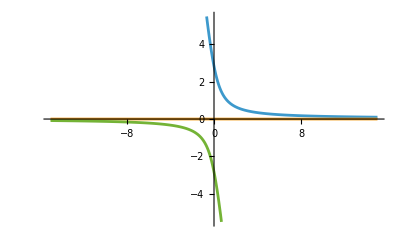

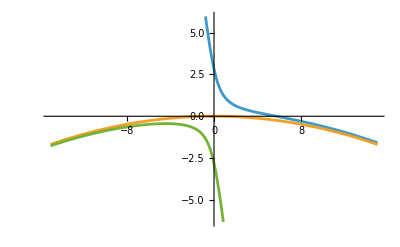

```mathematica
Plot[{ωAS[μ]-ωC[μ],ωC[μ]-ωC[μ],ωS[μ]-ωC[μ]}, {μ,-15,15}]
Plot[{ωAS[μ]-d1×μ,ωC[μ]-d1×μ,ωS[μ]-d1×μ}, {μ,-15,15}]
```

```mathematica
Plot[{bS[μ][[1]],bS[μ][[2]],bS[μ][[3]]},{μ,-15,15},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #1",PlotRange->Full,Frame->True, GridLines->Automatic,PlotLabels->{1,2,3}, PlotStyle->{Blue,Green,{Orange,Dashed}}]
Plot[{bC[μ][[1]],bC[μ][[2]],bC[μ][[3]]},{μ,-15,15},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #2",PlotRange->Full,Frame->True, GridLines->Automatic,PlotLabels->{1,2,3},PlotStyle->{Blue,Green,Orange}]
Plot[{bAS[μ][[1]],bAS[μ][[2]],bAS[μ][[3]]},{μ,-15,15},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #3",PlotRange->Full,Frame->True, GridLines->Automatic,PlotLabels->{1,2,3}, PlotStyle->{Blue,Green,{Orange,Dashed}}]
```

-Graphics-

-Graphics-

-Graphics-